# Retrospective evaluation of school-related measures on pre-vaccination dynamics of SARS-CoV-2

## Canfora B., Escosio R. A., Boldea O., van Dorp C. H., Nunes A., and Rozhnova G.

## Memory and global parameters

```mathematica
(* Clear *)
$HistoryLength=0;
ClearSystemCache[]
ClearAll["Global`*"]
Clear["Subscript"]
Clear["Superscript"]
Clear["Subsuperscript"]
Off[General::munfl]
memory:=Row[{"Memory Used:",MemoryInUse[]/1024^2.," MB"}]
SetDirectory[NotebookDirectory[]];
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"]
```

### PACKAGES AND PARAMETERS

```mathematica
(* External packages *)
AppendTo[$Path,"../packages"];
Needs["plottingFunctions`"];

(*ResourceFunction["DarkMode"][False]*)
(*ResourceFunction["GraphicsBrace"];*)


(* Notebook parameters *)
ifShowFigs = True;
ifExportData = True;
ifExportFigs = True;
exportFormat={".pdf",".eps"};

importExportScenarioResults[labelPrefix_,dataFunction_]:=Table[Module[{filePath,state},
filePath=FileNameJoin[{"../results"},StringJoin[labelPrefix,"_",scenarios[[i]],".wxf"]];
If[FileExistsQ[filePath],
state=Import[filePath,"WXF"];
state,
state=dataFunction[i];
Export[filePath,state,"WXF","CompressionLevel"->5];
state]],
{i,1,Length[scenarios]}];

exportFigs[figs_, filename_] := If[ifExportFigs,Table[Export[StringJoin["../figures/",filename, ToString[j],exportFormat⟦i⟧],figs⟦j⟧],{i,1,Length[exportFormat]},{j,1,Length[figs]}]];


(* Known constants*)
numAgeGroups = 10;
listAgeGroups= Table[k, {k, 1, numAgeGroups}];
listChildren = Range[1,3];
listAdults = Range[4,10];
groupIndex = {listChildren, listAdults};

numSamples = 2000;
stepSamples=20; (* 20 corresponds to 100 samples *)
listSamples=Table[i,{i,1,numSamples,stepSamples}];

numVariables=5;

(*scenarios={"Baseline", "Scenario1", "Scenario2", "Scenario1_RelaxedNS", "Scenario1_ZetaSchool","Scenario2_ZetaZetaS", "Scenario2_RelativeSchool"};*)
scenarios={"Baseline", "Scenario1", "Scenario2"};
(*scenarios={"Baseline"};*)
numScenarios = Length[scenarios];
```

```mathematica
memory
```

Memory Used:1296.49 MB

### IMPORTANT DATES AND TIME STEP

```mathematica
(* Date of starting simulations: February 25, 2020 *)
timeStart=0;
(* Date of start of the pandemic: February 26, 2020 *)

(* Date of last hospitalization/last data point: January 15, 2021 *)
timeEndData = Differences[{DateObject[{2020, 02, 26}],DateObject[{2021,01,15}]}]⟦1,1⟧+1+1 ; (* Jan 15 but starting with t=1 *)

(* Date of 2020 school vacation : June 10, 2020 *)
timeSchoolVacation=Differences[{DateObject[{2020, 02, 26}],DateObject[{2020, 06, 10}]}]⟦1,1⟧+1;

(* Integration end-time and time step*)
Subscript[t, step]=1;
Subscript[t, end]=timeEndData;
Subscript[t, start]=timeStart;
times =Range[Subscript[t, start],Subscript[t, end],Subscript[t, step]];
numTimes = Length[times];

Subscript[t, start,1]="February 25, 2020";
Subscript[t, end,1]="July 15, 2020";
Subscript[t, start,2]="July 15, 2020";
Subscript[t, end,2]="January 16, 2021";
```

## Demography and contact matrices

### CONTACT MATRICES FROM VESPIGNANI ET AL.

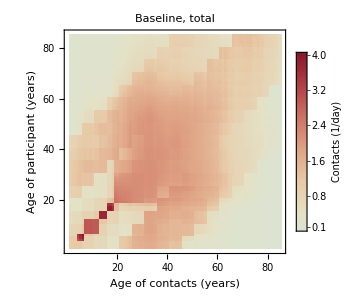
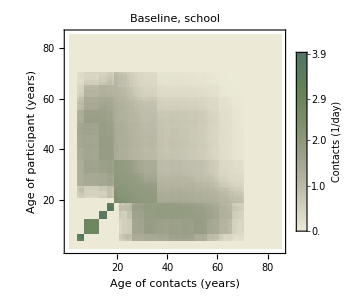
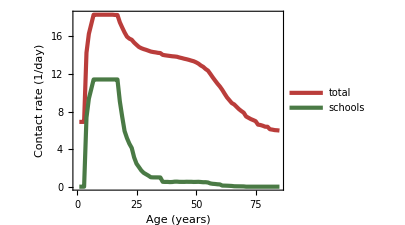
-Graphics- |  | -Graphics-
 | -Graphics- |

```mathematica
(* Importing Data *)
(* https://github.com/mobs-lab/mixing-patterns *)
schoolContactsMultiplier = 11.41;
demographyData85=Import["../data/PT_DEMOGRAPHY_DATA_85.csv"]⟦All,2⟧;
contactDataBefore85=Import["../data/PT_CONTACT_MATRIX_TOTAL_85.csv"];
schoolRawContactDataBefore85=  Import["../data/PT_CONTACT_MATRIX_SCHOOL_85.csv"];
schoolContactDataBefore85 = schoolContactsMultiplier * schoolRawContactDataBefore85;


(* Get the total contacts per participant *)
calculateTotalContsPerPar[conmat_, groupNo_] := Table[Total[conmat⟦k,All⟧],{k,groupNo}];
calculateContactsAgeGroups2=calculateTotalContsPerPar[contactDataBefore85, 85];
calculateSchoolContactsAgeGroups2=calculateTotalContsPerPar[schoolContactDataBefore85, 85];


(* Plotting *)figTotalContPerAge = plotThickLine[{calculateContactsAgeGroups2, calculateSchoolContactsAgeGroups2},{colorDarkRed, colorDarkGreen},"","Age (years)","Contact rate (1/day)",{"total", "schools"}];
figTotalConmat = plotMatrix[contactDataBefore85, "ThermometerColors" ,"Baseline, total", "contact"];
figSchoolConmat = plotMatrix[schoolContactDataBefore85, ColorData[{"AlpineColors", {1.15,0.45}}], "Baseline, school", "contact"];

figA = plotWithLetter[figTotalConmat, "A", "right"];
figB = plotWithLetter[figSchoolConmat, "B", "right"];
figC = plotWithLetter[figTotalContPerAge, "C", "right"];
figConts = Grid[{{figA,SpanFromLeft, figB}, {SpanFromLeft, figC, SpanFromLeft}}];
If[ifShowFigs, figConts]
```

### TRANSFORMING THE CONTACT MATRICES FROM 86x86 TO 10x10

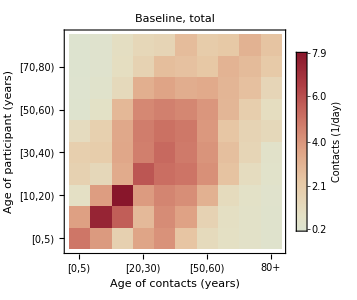
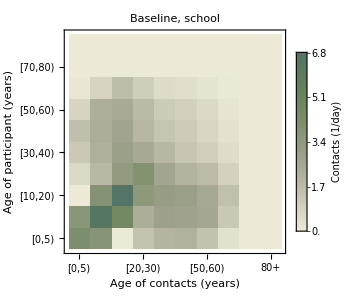
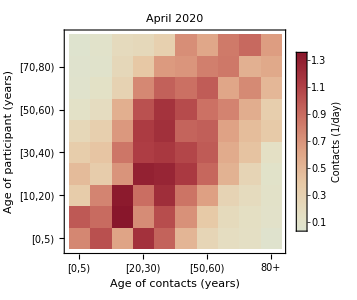
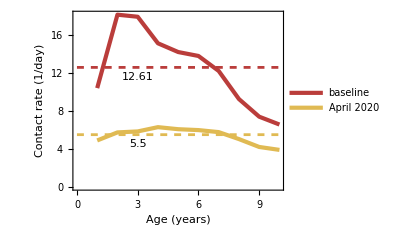
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
(* Demographic data for 86+
https://www.pordata.pt/Portugal/Popula%C3%A7%C3%A3o+residente++m%C3%A9dia+anual+total+e+por+grupo+et%C3%A1rio-10 *)
demog86Plus = 316442;

(* Getting the ratio of lockdown contacts based on NL data *)
contactDataNLBefore10=Import["../data/NL_CONTACT_MATRIX_BEFORE_10.csv"];
contactDataNLAfter10=Import["../data/NL_CONTACT_MATRIX_AFTER_10.csv"];
contactRatioNL10=contactDataNLAfter10/contactDataNLBefore10;
demographyData10=Flatten[Import["../data/PT_DEMOGRAPHY_DATA_10.xlsx"]];

(* Function transforming the 1x86 age groups to 1x10 *)
transformList86to10[list85_]:=Total/@Join[Partition[list85,5]⟦1;;2⟧,Partition[list85,10]⟦2;;⟧,{list85⟦81;;⟧}];
demographyData86=Append[demographyData85, demog86Plus];
demographyData10Derived=transformList86to10[demographyData86];


(* Creating the 86x86 contact matrices *)
transformMatrix85to86[mat85_]:=Join[Join[mat85,{mat85⟦85⟧}],List/@(Join[mat85,{mat85⟦85⟧}]⟦All,85⟧ demographyData86⟦86⟧/demographyData86⟦85⟧), 2];

contactDataBefore86=transformMatrix85to86[contactDataBefore85];
schoolContactDataBefore86=transformMatrix85to86[schoolContactDataBefore85];


(* Creating the 10x10 contact matrices*)
transformMatrix86to10[mat86_] :=transformList86to10[ Transpose[transformList86to10[Transpose[mat86]]] demographyData86]/demographyData10Derived;
contactDataBefore10=transformMatrix86to10[contactDataBefore86];
contactDataAfter10=contactDataBefore10 * contactRatioNL10 ;
schoolContactDataBefore10=transformMatrix86to10[schoolContactDataBefore86];


(* Assigning parameter variables *)
contactRates:=
Flatten[Table[{Subscript[b,{k,l}]->contactDataBefore10⟦k,l⟧,Subscript[a,{k,l}]->contactDataAfter10⟦k,l⟧,
Subscript[s, {k, l}]->schoolContactDataBefore10[[k,l]]},{k,1,numAgeGroups},{l,1,numAgeGroups}]];


(* Exporting data *)
If[ifExportData,
Export["../data/RES_PT_DEMOGRAPHY_DATA_86.csv",demographyData86,"Table"];Export["../data/RES_PT_DEMOGRAPHY_DATA_10.csv",demographyData10Derived,"Table"];
Export["../data/RES_PT_CONTACT_MATRIX_BEFORE_10.csv",contactDataBefore10,"Table"];
Export["../data/RES_PT_CONTACT_MATRIX_AFTER_10.csv",contactDataAfter10,"Table"];
Export["../data/RES_PT_CONTACT_MATRIX_BEFORE_86.csv",contactDataBefore86,"Table"];
Export["../data/RES_PT_CONTACT_MATRIX_SCHOOL_86.csv",schoolContactDataBefore86,"Table"];
Export["../data/RES_PT_CONTACT_MATRIX_SCHOOL_10.csv",schoolContactDataBefore10,"Table"]];


(* Get the total contacts per participant *)
calculateContactsAgeGroupsBefore=calculateTotalContsPerPar[contactDataBefore10, numAgeGroups];
calculateContactsAgeGroupsAfter=calculateTotalContsPerPar[contactDataAfter10, numAgeGroups];

calculateAverageContactRateBefore=Sum[calculateContactsAgeGroupsBefore⟦k⟧ *demographyData10⟦k⟧/Total[demographyData10],{k,listAgeGroups}];
calculateAverageContactRateAfter=Sum[calculateContactsAgeGroupsAfter⟦k⟧ *demographyData10⟦k⟧/Total[demographyData10],{k,listAgeGroups}];


(* Plotting *)
figContactMatrixBefore = plotMatrix[contactDataBefore10, "ThermometerColors" ,"Baseline, total", "contact"];
figSchoolContactMatrixBefore = plotMatrix[schoolContactDataBefore10, ColorData[{"AlpineColors", {1.15,0.45}}] ,"Baseline, school","contact"];
figContactMatrixAfter = plotMatrix[contactDataAfter10, "ThermometerColors", "April 2020", "contact"];
figTotalContPerAge =
Show[plotThickLine[{calculateContactsAgeGroupsBefore, calculateContactsAgeGroupsAfter},{colorDarkRed, colorYellow},"","Age (years)","Contact rate (1/day)",{"baseline", "April 2020"}],
plotYLine[calculateAverageContactRateBefore,0, 11,{3, calculateAverageContactRateBefore-0.5},{0.1, 0.9},colorDarkRed],
plotYLine[calculateAverageContactRateAfter,0, 11,{3, calculateAverageContactRateAfter-0.5},{0.1, 0.9},colorYellow]];

figA = plotWithLetter[figContactMatrixBefore, "A"];
figB = plotWithLetter[figSchoolContactMatrixBefore, "B"];
figC = plotWithLetter[figContactMatrixAfter, "C"];
figD = plotWithLetter[figTotalContPerAge, "D"];
figConts = Grid[{{figA, figB}, {figC, figD}}];
If[ifShowFigs, figConts]

figNames={"SFig1A","SFig1B","SFig1C"};
figArray={figA,figB,figC, figD};
If[ifExportFigs,Table[Export[StringJoin["../figures/",figNames⟦j⟧,exportFormat⟦i⟧],figArray⟦j⟧],{i,1,Length[exportFormat]},{j,1,Length[figNames]}]];
```

## Hospitalization data and estimated parameters

### ESTIMATED PARAMETERS

```mathematica
(* Importing estimated parameters *)
estimatesData=Import["../data/PARAMETER_ESTIMATES.csv"];
headerParameters=estimatesData⟦1⟧;
estimatesData=Drop[estimatesData,1];


(* Assigning parameters *)
probabOfTransmEpsilon[sample_]:=ϵ->estimatesData⟦sample,1⟧;
probabOfTransmZeta[sample_]:=ζ-> estimatesData⟦sample,2⟧;
hospitalizationRate[sample_]:=Table[Subscript[ν,k]->estimatesData⟦sample,2+k⟧,{k,1,numAgeGroups}];
susceptibility[sample_]:=Flatten[Join[
Table[Subscript[β,k]->estimatesData⟦sample,14⟧ ,{k,1,3}],
Table[Subscript[β,k]->estimatesData⟦sample,15⟧ ,{k,4,7}],
Table[Subscript[β,k]->estimatesData⟦sample,16⟧ ,{k,8,10}]]];
latencyRate[sample_]:=α->estimatesData⟦sample,18⟧;
recoveryRate[sample_]:=γ->estimatesData⟦sample,19⟧;
rOverDisp[sample_]:=estimatesData⟦sample,17⟧;
logFuncParams[sample_]:={Subscript[xx, 0]-> estimatesData⟦sample,20⟧,Subscript[K, 0]-> estimatesData⟦sample,21⟧,Subscript[xx, 1]-> estimatesData⟦sample,22⟧,Subscript[K, 1]-> estimatesData⟦sample,23⟧,Subscript[xx, 2]-> estimatesData⟦sample,24⟧,Subscript[K, 2]-> estimatesData⟦sample,25⟧,Subscript[xx, 3]-> estimatesData⟦sample,26⟧,Subscript[K, 3]-> estimatesData⟦sample,27⟧,Subscript[xx, 4]-> estimatesData⟦sample,28⟧,Subscript[K, 4]-> estimatesData⟦sample,29⟧};
uParams[sample_]:={Subscript[u, 1]-> estimatesData⟦sample,30⟧,Subscript[u, 2]-> estimatesData⟦sample,31⟧,Subscript[u, 3]-> estimatesData⟦sample,32⟧,Subscript[u, 4]-> estimatesData⟦sample,33⟧} ;
totalPop:=Table[Subscript[NN,k]-> demographyData10⟦k⟧,{k,listAgeGroups}];
initConds[sample_]:=Flatten[Table[{Subscript[S0,k]-> 1-estimatesData⟦sample,13⟧,Subscript[EE0,k]-> 0.5 estimatesData⟦sample,13⟧,Subscript[II0,k]-> 0.5 estimatesData⟦sample,13⟧,Subscript[R0,k]-> 0,Subscript[H0,k]-> 0},{k,listAgeGroups}]];


(* Table for all parameters *)
parameters[sample_]:=
Flatten[{contactRates,totalPop,probabOfTransmEpsilon[sample],probabOfTransmZeta[sample],hospitalizationRate[sample],initConds[sample],susceptibility[sample],logFuncParams[sample],uParams[sample],latencyRate[sample],recoveryRate[sample]}];

parameterConstVals = {estimatesData⟦All,1⟧ 100,estimatesData⟦All,2⟧,estimatesData⟦All,13⟧ Total[demographyData10],estimatesData⟦All,14⟧,estimatesData⟦All,15⟧,estimatesData⟦All,17⟧,1/estimatesData⟦All,18⟧,1/estimatesData⟦All,19⟧};
parameterTVals = {estimatesData⟦All,20⟧,estimatesData⟦All,22⟧,estimatesData⟦All,24⟧,estimatesData⟦All,26⟧,estimatesData⟦All,28⟧};
parameterKVals = {estimatesData⟦All,21⟧,estimatesData⟦All,23⟧,estimatesData⟦All,25⟧,estimatesData⟦All,27⟧,estimatesData⟦All,29⟧};
parameterUVals = {estimatesData⟦All,30⟧,estimatesData⟦All,31⟧,estimatesData⟦All,32⟧,estimatesData⟦All,33⟧};
parameterHospRateVals = Table[365 estimatesData⟦All,2+i⟧,{i,1,numAgeGroups}];
(*
Remove["plottingFunctions`*"]
Get["../packages/plottingFunctions.m"]
HISTOGRAM OF HOSPITALIZATION RATES
HISTOGRAM OF OTHER ESTIMATED PARAMETERS
PLOT OF LOGISTIC TRANSITIONS *)
```

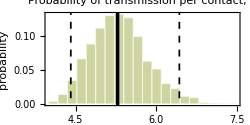
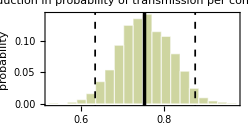
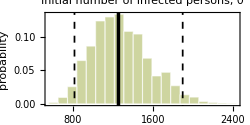
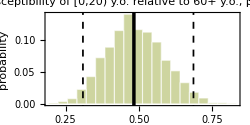
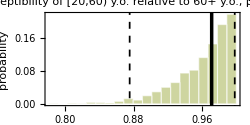
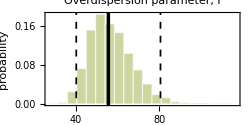
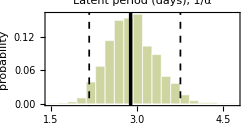
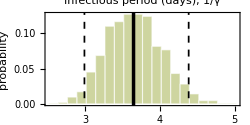
Grid[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]

```mathematica
Remove["plottingFunctions`*"]
Get["../packages/plottingFunctions.m"]
Grid[Table[Show[plotHistogram[parameterConstVals[[i]], parameterConstXLabel[[i]], parameterConstXLabelShort[[i]], "probability"]], {i, 1, Length[parameterConstVals]}]]
```

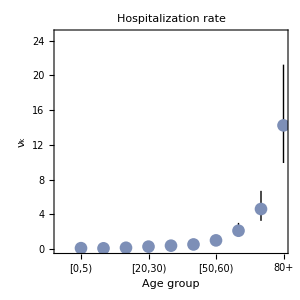
Grid[-Graphics-]

```mathematica
Remove["plottingFunctions`*"]
Get["../packages/plottingFunctions.m"]
medianQuantile[data_]:=Table[Around[Median[data[[i, All]]],{Abs[Median[data[[i, All]]]-Quantile[data[[i, All]],0.025]], Abs[Quantile[data[[i, All]], 0.975]-Median[data[[i, All]]]]}], {i, 1, Dimensions[data][[1]]}]

Grid[plotWithLetter[plotScatterWithError[parameterHospRateVals, ageLabelShort, "Age group", "ν_k","Hospitalization rate", True, Range[1, 7]], "A", "left"]]
```

### HOSPITALIZATION DATA

```mathematica
(* Importing data *)hospitalizationData=Import["../data/PT_HOSPITALIZATION_DATA.csv"];
hospitalizationData=Drop[hospitalizationData,1];


tickValues=DateRange[{2020,3,1},{2022,1,1},{4,"Month"}][[All,{1,2}]];
ticks={#,Rotate[DateString[DateObject[#],{"MonthNameShort"," ","Year"}],π/2]}&/@tickValues;
transitionDates=Table[DayPlus[{2020,02,25}, IntegerPart[Median[estimatesData⟦All,index⟧]]],{index,Range[20,28,2]}]; 
transitionDatesLabelsLong = {"First lockdown", "Relaxation after first lockdown", "Further relaxation", "Second lockdown", "Relaxation due to winter holidays"};
transitionDatesLabelsShort = {"LD 1", "Relax 1", "Relax 2", "LD 2", "Relax 3"};
(* Range[20,28,2] are the indices for transition dates *)

(*
Remove["plottingFunctions`*"]
Get["../packages/plottingFunctions.m"]
DIAGRAM FOR THE PAPER HERE *)
```

```mathematica
transitionDates
```

{Tue 24 Mar 2020,Tue 28 Apr 2020,Sat 22 Aug 2020,Wed 11 Nov 2020,Fri 18 Dec 2020}

## Scenarios

### SCHOOL REDUCTION FACTOR

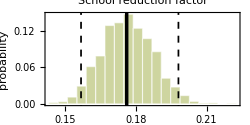

```mathematica
(* Calculation of the zeta_school parameter for Scenario 2 *)
schoolReductionEquation := 
Table[If[!(k==9 || k==10 ||l==9||l==10||(l==3 && k==1)||(l==1 && k==3)),Solve[(Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}])-reductionFactor Subscript[s,{k,l}]==(Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]),reductionFactor]⟦1⟧⟦1,2⟧],{k,1,numAgeGroups},{l,1,numAgeGroups}];
schoolReductionFactor[sample_]:=zetaSchools->Min[schoolReductionEquation /.Flatten[{contactRates,probabOfTransmZeta[sample],uParams[sample]}]][[1]];

(* Table for all parameters *)
parametersComplete[sample_]:=
Join[parameters[sample],{schoolReductionFactor[sample]}];



SRFFilePath = FileNameJoin[{"../results"},StringJoin["SCHOOL_REDUCTION_FACTOR.wxf"]];
schRedFacObtained= Module[{SRF},If[FileExistsQ[SRFFilePath],
SRF = Import[SRFFilePath,"WXF"],
SRF = Table[Min[schoolReductionEquation /.Flatten[{contactRates,probabOfTransmZeta[sample],uParams[sample]}]][[1]], {sample, 1, numSamples}];
Export[SRFFilePath,SRF,"WXF","CompressionLevel"->5];
SRF]];
(*Remove["plottingFunctions`*"]
Get["../packages/plottingFunctions.m"]*)
plotHistogram[schRedFacObtained, "School reduction factor", "ζ_s", "probability"]
```

### EXPRESSIONS FOR CONTACT MATRICES

```mathematica
contactMatrixBaseline[t_]:=
Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]);


(* SCENARIO 1 *)
(* Not closing schools during the first lockdown and closing them for school holidays on tstartschoolvacation (10 June)*)
(* ζ or Zeta schools can be introduced to reduce school contacts somewhat for the scenario with not closing schools after the first lockdown in 2020; the logic behind this is that there may be other measures implemented in schools such as masks, physical distancing, etc. *)
contactMatrixScenario1[t_]:=
(Subscript[b,{k,l}]-(*ζ*)Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+ (*ζ*) Subscript[s,{k,l}] (1-1/(1+Exp[-10 (t-timeSchoolVacation)]))+1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))(*(1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))*)+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]);

contactMatrixScenario1ZetaSchool[t_]:=
(Subscript[b,{k,l}]-(*ζ*)Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+ ζ 0.5*Subscript[s,{k,l}] (1-1/(1+Exp[-10 (t-timeSchoolVacation)]))+1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))(*(1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))*)+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]);

contactMatrixScenario1RelaxedNS[t_]:=
(Subscript[b,{k,l}]-(*ζ*)Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+ (*ζ*) Subscript[s,{k,l}] (1-1/(1+Exp[-10 (t-timeSchoolVacation)]))+1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]);


(* Scenario 2 *)
(* Not opening schools after the summer holidays in 2020 *)
(* Zeta schools must be used to make sure that contacts are non-negative for the scenario with not opening schools after the summer holidays in 2020 *)
contactMatrixScenario2[t_]:=
Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]-zetaSchools Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]-zetaSchools Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]-zetaSchools Subscript[s,{k,l}]); 

contactMatrixScenario2ZetaZetaS[t_]:=
Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]-ζ zetaSchools Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]-ζ zetaSchools Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]-ζ zetaSchools Subscript[s,{k,l}]); 

contactMatrixScenario2RelativeSchool[t_]:=
Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) ((Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}])-(Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}])* Subscript[s,{k,l}]/schoolContactsMultiplier) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) ((Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}])- (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}])*Subscript[s,{k,l}]/schoolContactsMultiplier)  (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) ((Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}])-(Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}])*Subscript[s,{k,l}]/schoolContactsMultiplier) ;
```

## Equations and variables

### MODEL EQUATIONS

```mathematica
varNumbers= Table[j, {j, 1, numVariables}];
eqNumbers=Table[k,{k,1,numAgeGroups numVariables}];

Table[{eq[Intervention_][1,k]:=Subscript[S,k]'[t]== - Subscript[λ,k][Intervention][t] Subscript[β,k] Subscript[S,k][t],eq[Intervention_][2,k]:=Subscript[EE,k]'[t]== Subscript[λ,k][Intervention][t] Subscript[β,k] Subscript[S,k][t]-α Subscript[EE,k][t],
eq[Intervention_][3,k]:=Subscript[II,k]'[t]== α Subscript[EE,k][t]-(γ +Subscript[ν,k]) Subscript[II,k][t],
eq[Intervention_][4,k]:=Subscript[R,k]'[t]==γ Subscript[II,k][t],
eq[Intervention_][5,k]:=Subscript[H,k]'[t]==Subscript[ν,k] Subscript[II,k][t]},{k,listAgeGroups}];

NNtot=Sum[Subscript[NN,k],{k,listAgeGroups}];

(*Table[Table[Subscript[λ,k][Intervention_/;Intervention==scenarios[[i]]][t]= ϵ Sum[scenarioContacts[[i]][t] (Subscript[II,l][t])/Subscript[NN,l],{l,listAgeGroups}],{k,listAgeGroups}], {i, 1, Length[scenarios]}];
*)
contactMatrixWhich[intervention_,t_]:=Which[intervention=="Baseline",contactMatrixBaseline[t],intervention=="Scenario1",contactMatrixScenario1[t],intervention=="Scenario2",contactMatrixScenario2[t],
intervention=="Scenario1_ZetaSchool",contactMatrixScenario1ZetaSchool[t],
intervention=="Scenario1_RelaxedNS",contactMatrixScenario1RelaxedNS[t],
intervention=="Scenario2_ZetaZetaS",contactMatrixScenario2ZetaZetaS[t],
intervention=="Scenario2_RelativeSchool",contactMatrixScenario2RelativeSchool[t],
True,$Failed ];

Table[Subscript[λ,k][intervention][t]=ε Sum[contactMatrixWhich[intervention,t] Subscript[II,l][t]/Subscript[NN,l],{l,listAgeGroups}],{k,listAgeGroups},{intervention,scenarios} (*Iterate over interventions*)];

eqs[Intervention_]:=Table[eq[Intervention][j,k],{j,numVariables},{k,listAgeGroups}];

eqsList[Intervention_]:=Flatten[Flatten[eqs[Intervention]]];
```

### VARIABLES

```mathematica
varsS=Table[Subscript[S,k][t],{k,listAgeGroups}];
varsEE=Table[Subscript[EE,k][t],{k,listAgeGroups}];
varsII=Table[Subscript[II,k][t],{k,listAgeGroups}];
varsR=Table[Subscript[R,k][t],{k,listAgeGroups}];
varsH=Table[Subscript[H,k][t],{k,listAgeGroups}];

totS=Total[Total[varsS]];
totEE=Total[Total[varsEE]];
totII=Total[Total[varsII]];
totR=Total[Total[varsR]];
totH=Total[Total[varsH]];

totVars={totS,totEE,totII,totR,totH};
totVarsYLabel={"S(t)","E(t)","I(t)","R(t)","H(t)"};

ageVars={Subscript[S,k][t],Subscript[EE,k][t],Subscript[II,k][t],Subscript[R,k][t],Subscript[H,k][t]};
ageVarsYlab={"S_k(t)","E_k(t)","I_k(t)","R_k(t)","H_k(t)"};

vars=Join[varsS,varsEE,varsII,varsR,varsH];
varsList=Flatten[vars];

hospVars=Table[Subscript[ν,k] (Subscript[II,k][t]),{k,listAgeGroups}];
infIncidenceVars=Table[α (Subscript[EE,k][t]),{k,listAgeGroups}];
```

### SOLVING THE MODEL

```mathematica
ICs=Table[ic[j,k],{j,varNumbers},{k,listAgeGroups}];
ICsList=Flatten[Flatten[ICs]];

Table[ic[1,k]=Subscript[S0,k] Subscript[NN,k]==Subscript[S,k][t]/.{t->Subscript[t, start]},{k,listAgeGroups}];
Table[ic[2,k]=Subscript[EE0,k] Subscript[NN,k]==Subscript[EE,k][t]/.{t->Subscript[t, start]},{k,listAgeGroups}];
Table[ic[3,k]=Subscript[II0,k] Subscript[NN,k]==Subscript[II,k][t]/.{t->Subscript[t, start]},{k,listAgeGroups}];
Table[ic[4,k]=Subscript[R0,k] Subscript[NN,k]==Subscript[R,k][t]/.{t->Subscript[t, start]},{k,listAgeGroups}];
Table[ic[5,k]=Subscript[H0,k] Subscript[NN,k]==Subscript[H,k][t]/.{t->Subscript[t, start]},{k,listAgeGroups}];


solution[Intervention_,pars_]:=NDSolve[Join[eqsList[Intervention],ICsList]/.pars,varsList,{t,Subscript[t, start],Subscript[t, end]}, Method->"StiffnessSwitching"];
```

### HOSPITALIZATIONS, INCIDENCES, AND SUSCEPTIBLES

```mathematica
parametersCompleteSampled = Table[parametersComplete[i],{i,1,numSamples,stepSamples}];


solutionsForLoop[i_]:=Table[solution[scenarios[[i]],parametersCompleteSampled[[j]]],{j,1,Length[listSamples]}];
solutionsScenarios = importExportScenarioResults["SOLUTIONS", solutionsForLoop];

trajectoriesVarForLoop[var_, i_, label_]:= 
Table[Table[Table[Evaluate[
(If[label === "SUSCEPTIBLE",
(If[k==1,(demographyData10⟦1⟧-86579)/demographyData10⟦1⟧,1] var⟦k⟧)+ If[k==1,86579,0],
var⟦k⟧]/.parametersCompleteSampled⟦j⟧)/.First@solutionsScenarios[[i]]⟦j⟧],
{t,Subscript[t, start],Subscript[t, end],Subscript[t, step]}],
{j,1,Length[listSamples]}],
{k,listAgeGroups}]; 
importExport4Trajectories[var_, label_] := Module[{func},
func[i_] := trajectoriesVarForLoop[var, i,label];
importExportScenarioResults[label, func]];


hospitalizationScenarios=importExport4Trajectories[hospVars, "HOSPITALIZATION"];
incidencesScenarios=importExport4Trajectories[infIncidenceVars, "INCIDENCE"];
susceptibleScenarios =importExport4Trajectories[varsS, "SUSCEPTIBLE"];


NBDReparameterized[m_,f_]:=NegativeBinomialDistribution[f,f/(f+m)];
hospSimulated[var_]:=Table[If[var⟦k⟧⟦sample⟧⟦t⟧>0,RandomVariate[NBDReparameterized[var⟦k⟧⟦sample⟧⟦t⟧,rOverDisp[listSamples⟦sample⟧]]],0],{k,listAgeGroups},{sample,1,Length[listSamples]},{t,1,Dimensions[var]⟦3⟧}];
hospitalizationSimulatedLoop[label_] := Module[{func},
func[i_] := hospSimulated[hospitalizationScenarios[[i]]];
     importExportScenarioResults[label, func]];
hospitalizationSimulatedScenarios = hospitalizationSimulatedLoop["HOSPITALIZATION_SIMULATED"];

summingGroups4Scenarios[variable_, index_] := Transpose[Table[Map[Total[#[[index[[i]], All, All]], {1}] &, variable], {i, 1, Length[index]}]];

hospitalizationScenariosGrouped = summingGroups4Scenarios[hospitalizationScenarios, groupIndex];
hospitalizationScenariosTotal = summingGroups4Scenarios[hospitalizationScenarios, {Range[1, 10]}];
incidencesScenariosGrouped = summingGroups4Scenarios[incidencesScenarios, groupIndex];
incidencesScenariosTotal = summingGroups4Scenarios[incidencesScenarios, {Range[1, 10]}];
susceptibleScenariosGrouped = summingGroups4Scenarios[susceptibleScenarios, groupIndex];
susceptibleScenariosTotal = summingGroups4Scenarios[susceptibleScenarios, {Range[1, 10]}];
hospitalizationSimulatedScenariosGrouped = summingGroups4Scenarios[hospitalizationSimulatedScenarios, groupIndex];
hospitalizationSimulatedScenariosTotal = summingGroups4Scenarios[hospitalizationSimulatedScenarios, {Range[1, 10]}];
```

```mathematica
Max[susceptibleScenariosGrouped[[1,1,All,All]]]
```

1.95121×10^6

```mathematica
Dimensions[susceptibleScenariosGrouped]
```

{3,2,100,327}

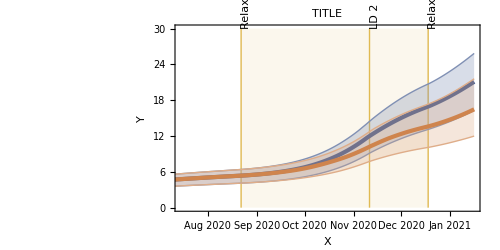

```mathematica
Remove["plottingFunctions`*"]
Get["../packages/plottingFunctions.m"]

(*Show[plotLineWithCrI[100-100susceptibleScenariosTotal[[1,1,All,All]]/Total[demographyData10],"TITLE","X","Y",colorBlue,Subscript[t, start,1], Subscript[t, end,1], {0, 30}],
plotLineWithCrI[100-100susceptibleScenariosTotal[[2,1,All,All]]/Total[demographyData10],"TITLE","X","Y",colorOrange,Subscript[t, start,1], Subscript[t, end,1], {0, 30}]]
Show[plotLineWithCrI[100-100susceptibleScenariosTotal[[1,1,All,All]]/Total[demographyData10],"TITLE","X","Y",colorBlue,Subscript[t, start,2], Subscript[t, end,2], {0, 30}],
plotLineWithCrI[100-100susceptibleScenariosTotal[[3,1,All,All]]/Total[demographyData10],"TITLE","X","Y",colorOrange,Subscript[t, start,2], Subscript[t, end,2], {0, 30}]]*)
(*Show[plotLineWithCrI[100-100susceptibleScenariosGrouped[[1,1,All,All]]/Total[demographyData10[[1;;3]]],"TITLE","X","Y",colorBlue,Subscript[t, start,1], Subscript[t, end,1], {0, 55}],
plotLineWithCrI[100-100susceptibleScenariosGrouped[[2,1,All,All]]/Total[demographyData10[[1;;3]]],"TITLE","X","Y",colorOrange,Subscript[t, start,1], Subscript[t, end,1], {0, 55}]]
Show[plotLineWithCrI[100-100susceptibleScenariosGrouped[[1,1,All,All]]/Total[demographyData10[[1;;3]]],"TITLE","X","Y",colorBlue,Subscript[t, start,2], Subscript[t, end,2], {0, 20}],
plotLineWithCrI[100-100susceptibleScenariosGrouped[[3,1,All,All]]/Total[demographyData10[[1;;3]]],"TITLE","X","Y",colorOrange,Subscript[t, start,2], Subscript[t, end,2], {0, 20}]]*)
Show[plotLineWithCrI[100-100susceptibleScenariosGrouped[[1,2,All,All]]/Total[demographyData10[[4;;10]]],"TITLE","X","Y",colorBlue,Subscript[t, start,2], Subscript[t, end,2],ticksss, {0, 30}],
plotLineWithCrI[100-100susceptibleScenariosGrouped[[3,2,All,All]]/Total[demographyData10[[4;;10]]],"TITLE","X","Y",colorOrange,Subscript[t, start,2], Subscript[t, end,2], ticksss,{0, 30}]]
```

## Analysis

### AVERAGE CONTACT RATE

```mathematica
trajectoriesContacts[i_, t_, sample_]:=Table[Table[contactMatrixWhich[scenarios[[i]],t]/.parametersCompleteSampled⟦sample⟧/.contactRates, {l, 1, numAgeGroups}], {k, 1, numAgeGroups}];

importExport4Contacts[label_] := Module[{func},
func[i_] := Table[Table[trajectoriesContacts[i, t, j],{t,Subscript[t, start],Subscript[t, end],Subscript[t, step]}],{j,1,Length[listSamples]}];
importExportScenarioResults[label, func]];
contactMatricesScenarios = importExport4Contacts["CONTACTS"];
```

```mathematica
contactMatricesScenarios[[2,100,301]]//MatrixForm
```

(1.48023 | 1.22825 | 0.516849 | 1.21474 | 1.23253 | 0.648997 | 0.249849 | 0.180883 | 0.146364 | 0.0965574
1.1423 | 3.62647 | 2.22919 | 0.804903 | 1.34223 | 1.02139 | 0.38489 | 0.200377 | 0.148852 | 0.10291
0.239213 | 1.11046 | 4.28619 | 1.16436 | 1.50729 | 1.26699 | 0.840069 | 0.253545 | 0.170096 | 0.106742
0.449869 | 0.320856 | 0.933788 | 2.35367 | 1.8263 | 1.65937 | 1.25863 | 0.667737 | 0.238002 | 0.11481
0.392058 | 0.459016 | 1.03412 | 1.56397 | 1.84149 | 1.57951 | 1.22641 | 0.688456 | 0.384925 | 0.126343
0.229095 | 0.387372 | 0.964487 | 1.57582 | 1.74992 | 1.52463 | 1.20474 | 0.692664 | 0.424926 | 0.307268
0.103053 | 0.170691 | 0.748402 | 1.39805 | 1.59106 | 1.4085 | 1.18399 | 0.851872 | 0.505419 | 0.263212
0.0917689 | 0.109293 | 0.277624 | 0.912311 | 1.09881 | 0.993329 | 1.04795 | 0.797385 | 0.753905 | 0.431129
0.0900819 | 0.0984123 | 0.224696 | 0.392085 | 0.739295 | 0.729699 | 0.743726 | 0.905383 | 0.724841 | 0.631997
0.0867488 | 0.0991985 | 0.206485 | 0.277187 | 0.35574 | 0.774465 | 0.569371 | 0.75685 | 0.926022 | 0.705836)

```mathematica
(*summingContacts[ageindex_] := Table[Table[Table[Sum[trajectoriesTotalContacts[[i,t,j]][[k]]demographyData10⟦k⟧/Total[demographyData10],{k,ageindex}],{t,Subscript[t, start],Subscript[t, end],Subscript[t, step]}],{j,1,Length[listSamples]}], {i, 1, Length[scenarios]}];

contactMatrices = {contactMatrixBaseline, contactMatrixScenario1, contactMatrixScenario2};

contactMatricesTotal = importExport4Contacts[contactMatrices, listAgeGroups, "TOTAL_CONTACTS"];
contactMatricesChildren = importExport4Contacts[contactMatrices, listChildren, "CHILDREN_CONTACTS"];
contactMatricesAdults = importExport4Contacts[contactMatrices, listAdults, "ADULTS_CONTACTS"];

(*plotLineWithCrI[, "TITLE", "XLABEL", "YLABEL", {colorBlue, colorOrange}, Subscript[t, start,1], Subscript[t, end,1]]*)*)
```

### TIME-VARYING REPRODUCTION NUMBER

```mathematica
eqNumbersSusceptible = eqNumbers[[1 ;; numAgeGroups]];
eqNumbersExposed = eqNumbers[[numAgeGroups + 1 ;; 2 numAgeGroups]];
eqNumbersInfectious = eqNumbers[[2 numAgeGroups + 1 ;; 3 numAgeGroups]];

NGM= Table[Table[((-1/D[eqsList[scenarios[[i]]]⟦p,2⟧,varsList⟦p⟧] D[eqsList[scenarios[[i]]]⟦k,2⟧,varsList⟦p⟧])),{k,eqNumbersExposed},{p,eqNumbersInfectious}], {i, 1, Length[scenarios]}];
```

```mathematica
substituteNGM[scenNum_, sample_, time_] :=
((NGM[[scenNum]]/. (First@solutionsScenarios[[scenNum]][[sample]])[[eqNumbersSusceptible]]) /. parametersCompleteSampled[[sample]]) /. t -> time;

NGMForLoop[i_] :=Table[Table[substituteNGM[i, j, t], {t,Subscript[t, start],Subscript[t, end],Subscript[t, step]}],{j,1,Length[listSamples]}];
NGMScenarios = importExportScenarioResults["NGM", NGMForLoop];

eigenAllFirst[matrix_] := Module[{valRight, valLeft}, 
valRight = Eigensystem[matrix, 1];
valLeft = Eigensystem[Transpose[matrix], 1]; 
{valRight[[1]][[1]], 
valRight[[2]][[1]],
valLeft[[2]][[1]]}];
RtForLoop[i_] :=Table[Table[eigenAllFirst[NGMScenarios[[i, j, t]]], {t,1, numTimes}],{j,1,Length[listSamples]}];
RtScenarios = importExportScenarioResults["EIGEN", RtForLoop];
```

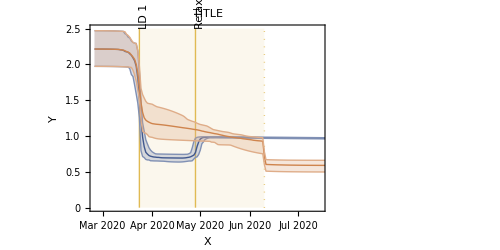

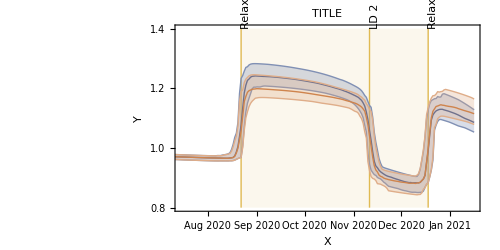

```mathematica
(*Show[DateListPlot[Table[Median[RtScenarios[[1,All,t,1]]],{t,1, numTimes}], {"February 25, 2020",Automatic,{0,0,1}}],
DateListPlot[Table[Median[RtScenarios[[2,All,t,1]]],{t,1, numTimes}],{"February 25, 2020",Automatic,{0,0,1}}, PlotStyle->Gray], PlotRange->All]*)
Remove["plottingFunctions`*"]
Get["../packages/plottingFunctions.m"]

(*Show[plotLineWithCrI[RtScenarios[[1,All,All,1]],"TITLE","X","Y",colorBlue,Subscript[t, start,1], Subscript[t, end,1],{0, 2.5}],
plotLineWithCrI[RtScenarios[[2,All,All,1]],"TITLE","X","Y",colorOrange,Subscript[t, start,1], Subscript[t, end,1],{0, 2.5}],
plotLineWithCrI[RtScenarios[[4,All,All,1]],"TITLE","X","Y",colorYellowGreen,Subscript[t, start,1], Subscript[t, end,1],{0, 2.5}],
plotLineWithCrI[RtScenarios[[5,All,All,1]],"TITLE","X","Y",colorDarkGreen,Subscript[t, start,1], Subscript[t, end,1],{0, 2.5}]]

Show[plotLineWithCrI[RtScenarios[[1,All,All,1]],"TITLE","X","Y",colorBlue,Subscript[t, start,2], Subscript[t, end,2],{0.8, 1.3}],
plotLineWithCrI[RtScenarios[[3,All,All,1]],"TITLE","X","Y",colorOrange,Subscript[t, start,2], Subscript[t, end,2],{0.8, 1.3}],
plotLineWithCrI[RtScenarios[[6,All,All,1]],"TITLE","X","Y",colorYellow,Subscript[t, start,2], Subscript[t, end,2],{0.8, 1.3}],
plotLineWithCrI[RtScenarios[[7,All,All,1]],"TITLE","X","Y",colorDarkGreen,Subscript[t, start,2], Subscript[t, end,2] ,{0.8, 1.3}]]*)

Show[plotLineWithCrI[RtScenarios[[1,All,All,1]],"TITLE","X","Y",colorBlue,Subscript[t, start,1], Subscript[t, end,1],{0, 2.5}],
plotLineWithCrI[RtScenarios[[2,All,All,1]],"TITLE","X","Y",colorOrange,Subscript[t, start,1], Subscript[t, end,1],{0, 2.5}]]

Show[plotLineWithCrI[RtScenarios[[1,All,All,1]],"TITLE","X","Y",colorBlue,Subscript[t, start,2], Subscript[t, end,2],{0.8, 1.4}],
plotLineWithCrI[RtScenarios[[3,All,All,1]],"TITLE","X","Y",colorOrange,Subscript[t, start,2], Subscript[t, end,2],{0.8, 1.4}]]
```

### TIME-VARYING CUMULATIVE ELASTICITIES

```mathematica
sensMatrix[eigen_]:=
Module[{eigenRight, eigenLeft},
eigenRight = eigen[[2]];
eigenLeft = eigen[[3]];Outer[Times,eigenLeft,eigenRight]/Dot[eigenLeft, eigenRight]];

elasMatrix[eigen_, NGM_, sens_] := 
Module[{R},
R = eigen[[1]];
NGM * sens / R];

cumuElasMatrix[elas_] :=
Total[elas,{1}];

sensForLoop[i_] :=Table[Table[sensMatrix[RtScenarios[[i, j, t]]], {t,1, numTimes}],{j,1,Length[listSamples]}];
elasForLoop[i_] :=Table[Table[elasMatrix[RtScenarios[[i, j, t]], NGMScenarios[[i, j, t]], sensScenarios[[i, j, t]]], {t,1, numTimes}],{j,1,Length[listSamples]}];
cumuElasForLoop[i_] := Table[Table[cumuElasMatrix[elasScenarios[[i, j, t]]], {t,1, numTimes}],{j,1,Length[listSamples]}];

sensScenarios = importExportScenarioResults["SENSITIVITY", sensForLoop];
elasScenarios = importExportScenarioResults["ELASTICITY", elasForLoop];
cumuElasScenarios = importExportScenarioResults["CUMUELAS", cumuElasForLoop];


cumuElasGroupedScenarios = Table[Table[Total[cumuElasScenarios[[scen]][[sample]][[time]][[groupIndex[[i]]]]], {i, 1, Length[groupIndex]}], {scen, 1, Length[scenarios]}, {sample, 1, Length[listSamples]}, {time, 1, numTimes}];
```

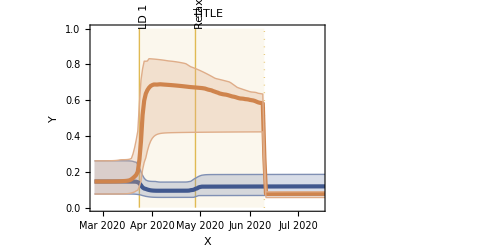

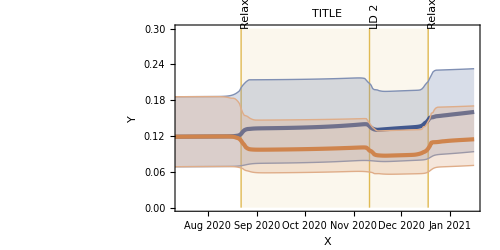

```mathematica
tickValues=DateRange[{2020,3,1},{2021,1,1},{1,"Month"}][[All,{1,2}]];
ticksss={#,Rotate[DateString[#,{"MonthNameShort"," ","Year"}],π/2]}&/@tickValues;
(*tickValues=DateRange[{2020,3,1},{2021,1,1},{1,"Month"}];*)
(*ticksss={#,DateString[#,{"MonthNameShort"," ","Year"}]}&/@tickValues;*)



Remove["plottingFunctions`*"]
Get["../packages/plottingFunctions.m"]

Show[plotLineWithCrI[cumuElasGroupedScenarios[[1,All,All,1]],"TITLE","X","Y",colorBlue,Subscript[t, start,1], Subscript[t, end,1],ticksss,{0, 1}],
plotLineWithCrI[cumuElasGroupedScenarios[[2,All,All,1]],"TITLE","X","Y",colorOrange,Subscript[t, start,1], Subscript[t, end,1],ticksss,{0, 1}]]

Show[plotLineWithCrI[cumuElasGroupedScenarios[[1,All,All,1]],"TITLE","X","Y",colorBlue,Subscript[t, start,2], Subscript[t, end,2],ticksss,{0, 0.3}],
plotLineWithCrI[cumuElasGroupedScenarios[[3,All,All,1]],"TITLE","X","Y",colorOrange,Subscript[t, start,2], Subscript[t, end,2],ticksss,{0, 0.3}]]
```

```mathematica
E
```

### PARAMETER ELASTICITIES

```mathematica
susceptibilitySymbol = Table[Subscript[β,k], {k, 1, numAgeGroups}];
hospitalizationRateSymbol = Table[Subscript[ν,k], {k, 1, numAgeGroups}];
contactSymbol = Table[Subscript[c, {k, l}], {k, 1, numAgeGroups}, {l, 1, numAgeGroups}];
(*parameterSymbols = {susceptibilitySymbol, hospitalizationRateSymbol, contactSymbol};*)
parameterSymbols = {susceptibilitySymbol};
parameterSymbols = Flatten[parameterSymbols];

NGMContactInvariant = Table[NGM[[1]][[k]] /. {Table[contactMatrixBaseline[t] -> Subscript[c, {k, l}],{l, 1, numAgeGroups}]}[[1]], {k, 1, numAgeGroups}];
NGMContactInvariant = Simplify[NGMContactInvariant];

NGMContactInvariant // MatrixForm
```

((ε c_{1,1} β_1 S_1[t])/(NN_1 (γ+ν_1)) | (ε c_{1,2} β_1 S_1[t])/(NN_2 (γ+ν_2)) | (ε c_{1,3} β_1 S_1[t])/(NN_3 (γ+ν_3)) | (ε c_{1,4} β_1 S_1[t])/(NN_4 (γ+ν_4)) | (ε c_{1,5} β_1 S_1[t])/(NN_5 (γ+ν_5)) | (ε c_{1,6} β_1 S_1[t])/(NN_6 (γ+ν_6)) | (ε c_{1,7} β_1 S_1[t])/(NN_7 (γ+ν_7)) | (ε c_{1,8} β_1 S_1[t])/(NN_8 (γ+ν_8)) | (ε c_{1,9} β_1 S_1[t])/(NN_9 (γ+ν_9)) | (ε c_{1,10} β_1 S_1[t])/(NN_10 (γ+ν_10))
(ε c_{2,1} β_2 S_2[t])/(NN_1 (γ+ν_1)) | (ε c_{2,2} β_2 S_2[t])/(NN_2 (γ+ν_2)) | (ε c_{2,3} β_2 S_2[t])/(NN_3 (γ+ν_3)) | (ε c_{2,4} β_2 S_2[t])/(NN_4 (γ+ν_4)) | (ε c_{2,5} β_2 S_2[t])/(NN_5 (γ+ν_5)) | (ε c_{2,6} β_2 S_2[t])/(NN_6 (γ+ν_6)) | (ε c_{2,7} β_2 S_2[t])/(NN_7 (γ+ν_7)) | (ε c_{2,8} β_2 S_2[t])/(NN_8 (γ+ν_8)) | (ε c_{2,9} β_2 S_2[t])/(NN_9 (γ+ν_9)) | (ε c_{2,10} β_2 S_2[t])/(NN_10 (γ+ν_10))
(ε c_{3,1} β_3 S_3[t])/(NN_1 (γ+ν_1)) | (ε c_{3,2} β_3 S_3[t])/(NN_2 (γ+ν_2)) | (ε c_{3,3} β_3 S_3[t])/(NN_3 (γ+ν_3)) | (ε c_{3,4} β_3 S_3[t])/(NN_4 (γ+ν_4)) | (ε c_{3,5} β_3 S_3[t])/(NN_5 (γ+ν_5)) | (ε c_{3,6} β_3 S_3[t])/(NN_6 (γ+ν_6)) | (ε c_{3,7} β_3 S_3[t])/(NN_7 (γ+ν_7)) | (ε c_{3,8} β_3 S_3[t])/(NN_8 (γ+ν_8)) | (ε c_{3,9} β_3 S_3[t])/(NN_9 (γ+ν_9)) | (ε c_{3,10} β_3 S_3[t])/(NN_10 (γ+ν_10))
(ε c_{4,1} β_4 S_4[t])/(NN_1 (γ+ν_1)) | (ε c_{4,2} β_4 S_4[t])/(NN_2 (γ+ν_2)) | (ε c_{4,3} β_4 S_4[t])/(NN_3 (γ+ν_3)) | (ε c_{4,4} β_4 S_4[t])/(NN_4 (γ+ν_4)) | (ε c_{4,5} β_4 S_4[t])/(NN_5 (γ+ν_5)) | (ε c_{4,6} β_4 S_4[t])/(NN_6 (γ+ν_6)) | (ε c_{4,7} β_4 S_4[t])/(NN_7 (γ+ν_7)) | (ε c_{4,8} β_4 S_4[t])/(NN_8 (γ+ν_8)) | (ε c_{4,9} β_4 S_4[t])/(NN_9 (γ+ν_9)) | (ε c_{4,10} β_4 S_4[t])/(NN_10 (γ+ν_10))
(ε c_{5,1} β_5 S_5[t])/(NN_1 (γ+ν_1)) | (ε c_{5,2} β_5 S_5[t])/(NN_2 (γ+ν_2)) | (ε c_{5,3} β_5 S_5[t])/(NN_3 (γ+ν_3)) | (ε c_{5,4} β_5 S_5[t])/(NN_4 (γ+ν_4)) | (ε c_{5,5} β_5 S_5[t])/(NN_5 (γ+ν_5)) | (ε c_{5,6} β_5 S_5[t])/(NN_6 (γ+ν_6)) | (ε c_{5,7} β_5 S_5[t])/(NN_7 (γ+ν_7)) | (ε c_{5,8} β_5 S_5[t])/(NN_8 (γ+ν_8)) | (ε c_{5,9} β_5 S_5[t])/(NN_9 (γ+ν_9)) | (ε c_{5,10} β_5 S_5[t])/(NN_10 (γ+ν_10))
(ε c_{6,1} β_6 S_6[t])/(NN_1 (γ+ν_1)) | (ε c_{6,2} β_6 S_6[t])/(NN_2 (γ+ν_2)) | (ε c_{6,3} β_6 S_6[t])/(NN_3 (γ+ν_3)) | (ε c_{6,4} β_6 S_6[t])/(NN_4 (γ+ν_4)) | (ε c_{6,5} β_6 S_6[t])/(NN_5 (γ+ν_5)) | (ε c_{6,6} β_6 S_6[t])/(NN_6 (γ+ν_6)) | (ε c_{6,7} β_6 S_6[t])/(NN_7 (γ+ν_7)) | (ε c_{6,8} β_6 S_6[t])/(NN_8 (γ+ν_8)) | (ε c_{6,9} β_6 S_6[t])/(NN_9 (γ+ν_9)) | (ε c_{6,10} β_6 S_6[t])/(NN_10 (γ+ν_10))
(ε c_{7,1} β_7 S_7[t])/(NN_1 (γ+ν_1)) | (ε c_{7,2} β_7 S_7[t])/(NN_2 (γ+ν_2)) | (ε c_{7,3} β_7 S_7[t])/(NN_3 (γ+ν_3)) | (ε c_{7,4} β_7 S_7[t])/(NN_4 (γ+ν_4)) | (ε c_{7,5} β_7 S_7[t])/(NN_5 (γ+ν_5)) | (ε c_{7,6} β_7 S_7[t])/(NN_6 (γ+ν_6)) | (ε c_{7,7} β_7 S_7[t])/(NN_7 (γ+ν_7)) | (ε c_{7,8} β_7 S_7[t])/(NN_8 (γ+ν_8)) | (ε c_{7,9} β_7 S_7[t])/(NN_9 (γ+ν_9)) | (ε c_{7,10} β_7 S_7[t])/(NN_10 (γ+ν_10))
(ε c_{8,1} β_8 S_8[t])/(NN_1 (γ+ν_1)) | (ε c_{8,2} β_8 S_8[t])/(NN_2 (γ+ν_2)) | (ε c_{8,3} β_8 S_8[t])/(NN_3 (γ+ν_3)) | (ε c_{8,4} β_8 S_8[t])/(NN_4 (γ+ν_4)) | (ε c_{8,5} β_8 S_8[t])/(NN_5 (γ+ν_5)) | (ε c_{8,6} β_8 S_8[t])/(NN_6 (γ+ν_6)) | (ε c_{8,7} β_8 S_8[t])/(NN_7 (γ+ν_7)) | (ε c_{8,8} β_8 S_8[t])/(NN_8 (γ+ν_8)) | (ε c_{8,9} β_8 S_8[t])/(NN_9 (γ+ν_9)) | (ε c_{8,10} β_8 S_8[t])/(NN_10 (γ+ν_10))
(ε c_{9,1} β_9 S_9[t])/(NN_1 (γ+ν_1)) | (ε c_{9,2} β_9 S_9[t])/(NN_2 (γ+ν_2)) | (ε c_{9,3} β_9 S_9[t])/(NN_3 (γ+ν_3)) | (ε c_{9,4} β_9 S_9[t])/(NN_4 (γ+ν_4)) | (ε c_{9,5} β_9 S_9[t])/(NN_5 (γ+ν_5)) | (ε c_{9,6} β_9 S_9[t])/(NN_6 (γ+ν_6)) | (ε c_{9,7} β_9 S_9[t])/(NN_7 (γ+ν_7)) | (ε c_{9,8} β_9 S_9[t])/(NN_8 (γ+ν_8)) | (ε c_{9,9} β_9 S_9[t])/(NN_9 (γ+ν_9)) | (ε c_{9,10} β_9 S_9[t])/(NN_10 (γ+ν_10))
(ε c_{10,1} β_10 S_10[t])/(NN_1 (γ+ν_1)) | (ε c_{10,2} β_10 S_10[t])/(NN_2 (γ+ν_2)) | (ε c_{10,3} β_10 S_10[t])/(NN_3 (γ+ν_3)) | (ε c_{10,4} β_10 S_10[t])/(NN_4 (γ+ν_4)) | (ε c_{10,5} β_10 S_10[t])/(NN_5 (γ+ν_5)) | (ε c_{10,6} β_10 S_10[t])/(NN_6 (γ+ν_6)) | (ε c_{10,7} β_10 S_10[t])/(NN_7 (γ+ν_7)) | (ε c_{10,8} β_10 S_10[t])/(NN_8 (γ+ν_8)) | (ε c_{10,9} β_10 S_10[t])/(NN_9 (γ+ν_9)) | (ε c_{10,10} β_10 S_10[t])/(NN_10 (γ+ν_10)))

```mathematica
betaVals = {susceptibilityVals[[1, listSamples]], susceptibilityVals[[1, listSamples]], susceptibilityVals[[1, listSamples]], susceptibilityVals[[2, listSamples]], susceptibilityVals[[2, listSamples]], susceptibilityVals[[2, listSamples]], susceptibilityVals[[2, listSamples]], susceptibilityVals[[3, listSamples]], susceptibilityVals[[3, listSamples]], susceptibilityVals[[3, listSamples]]};
Table[susceptibilityVals[[1, 1]], {i, 1, 10}]
```

Part::partd: Part specification susceptibilityVals⟦1,{1,21,41,61,81,101,121,141,161,181,201,221,241,261,281,301,321,341,361,381,401,421,441,461,481,501,521,541,561,581,601,621,641,661,681,701,721,741,761,781,801,821,841,861,881,901,921,941,961,981,«50»}⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification susceptibilityVals⟦1,1⟧ is longer than depth of object.

{susceptibilityVals⟦1,1⟧,susceptibilityVals⟦1,1⟧,susceptibilityVals⟦1,1⟧,susceptibilityVals⟦1,1⟧,susceptibilityVals⟦1,1⟧,susceptibilityVals⟦1,1⟧,susceptibilityVals⟦1,1⟧,susceptibilityVals⟦1,1⟧,susceptibilityVals⟦1,1⟧,susceptibilityVals⟦1,1⟧}

```mathematica
Dimensions[NGMScenarios]
```

{3,100,327,10,10}

```mathematica
Dimensions[betaVals]
```

{10}

```mathematica
Dimensions[elasScenarios]
```

{3,100,327,10,10}

```mathematica
susceptibilityVals={estimatesData⟦All,14⟧ ,estimatesData⟦All,15⟧ ,estimatesData⟦All,16⟧};
```

```mathematica
contactRates
```

{b_{1,1}→2.54599,a_{1,1}→0.66379,s_{1,1}→1.94146,b_{1,2}→1.79557,a_{1,2}→0.896331,s_{1,2}→1.29028,b_{1,3}→0.597741,a_{1,3}→0.549225,s_{1,3}→0.,b_{1,4}→1.58124,a_{1,4}→1.09857,s_{1,4}→0.0253809,b_{1,5}→1.88037,a_{1,5}→0.813849,s_{1,5}→0.0592522,b_{1,6}→0.976327,a_{1,6}→0.443574,s_{1,6}→0.0914605,b_{1,7}→0.37358,a_{1,7}→0.173255,s_{1,7}→0.0256729,b_{1,8}→0.285957,a_{1,8}→0.108539,s_{1,8}→0.00205149,b_{1,9}→0.228345,a_{1,9}→0.0911416,s_{1,9}→0.,b_{1,10}→0.158905,a_{1,10}→0.0511191,s_{1,10}→0.,b_{2,1}→1.66701,a_{2,1}→0.836786,s_{2,1}→1.1979,b_{2,2}→7.00627,a_{2,2}→0.788293,s_{2,2}→6.37547,b_{2,3}→3.50534,a_{2,3}→1.35811,s_{2,3}→2.70494,b_{2,4}→1.12103,a_{2,4}→0.648049,s_{2,4}→0.104617,b_{2,5}→2.02307,a_{2,5}→0.913181,s_{2,5}→0.287726,b_{2,6}→1.60218,a_{2,6}→0.626547,s_{2,6}→0.286894,b_{2,7}→0.570874,a_{2,7}→0.271936,s_{2,7}→0.22302,b_{2,8}→0.30405,a_{2,8}→0.134109,s_{2,8}→0.0201486,b_{2,9}→0.228345,a_{2,9}→0.0969225,s_{2,9}→0.,b_{2,10}→0.158905,a_{2,10}→0.0658767,s_{2,10}→0.,b_{3,1}→0.277096,a_{3,1}→0.253713,s_{3,1}→0.,b_{3,2}→1.7503,a_{3,2}→0.672021,s_{3,2}→1.35064,b_{3,3}→7.92572,a_{3,3}→1.31878,s_{3,3}→6.80854,b_{3,4}→1.77052,a_{3,4}→0.775213,s_{3,4}→0.924351,b_{3,5}→2.18543,a_{3,5}→1.11967,s_{3,5}→0.487979,b_{3,6}→2.00318,a_{3,6}→0.760043,s_{3,6}→0.356924,b_{3,7}→1.28105,a_{3,7}→0.555326,s_{3,7}→0.222397,b_{3,8}→0.368414,a_{3,8}→0.187472,s_{3,8}→0.0313604,b_{3,9}→0.243935,a_{3,9}→0.129283,s_{3,9}→0.,b_{3,10}→0.163057,a_{3,10}→0.070255,s_{3,10}→0.,b_{4,1}→0.591971,a_{4,1}→0.399902,s_{4,1}→0.00950192,b_{4,2}→0.45205,a_{4,2}→0.252689,s_{4,2}→0.0421863,b_{4,3}→1.42984,a_{4,3}→0.610879,s_{4,3}→0.746488,b_{4,4}→3.86932,a_{4,4}→1.25055,s_{4,4}→1.42563,b_{4,5}→2.78535,a_{4,5}→1.20687,s_{4,5}→0.246543,b_{4,6}→2.57546,a_{4,6}→1.04786,s_{4,6}→0.0608675,b_{4,7}→1.94659,a_{4,7}→0.802298,s_{4,7}→0.0355611,b_{4,8}→0.985505,a_{4,8}→0.477108,s_{4,8}→0.0120944,b_{4,9}→0.3383,a_{4,9}→0.184186,s_{4,9}→0.,b_{4,10}→0.187177,a_{4,10}→0.0627074,s_{4,10}→0.,b_{5,1}→0.60404,a_{5,1}→0.252438,s_{5,1}→0.0190338,b_{5,2}→0.699997,a_{5,2}→0.303404,s_{5,2}→0.0995556,b_{5,3}→1.5144,a_{5,3}→0.751813,s_{5,3}→0.338147,b_{5,4}→2.39,a_{5,4}→1.02836,s_{5,4}→0.211549,b_{5,5}→2.96178,a_{5,5}→1.04986,s_{5,5}→0.0497481,b_{5,6}→2.49673,a_{5,6}→0.948123,s_{5,6}→0.0220656,b_{5,7}→1.84907,a_{5,7}→0.833753,s_{5,7}→0.0135955,b_{5,8}→1.00521,a_{5,8}→0.50376,s_{5,8}→0.00271788,b_{5,9}→0.525449,a_{5,9}→0.321531,s_{5,9}→0.,b_{5,10}→0.191036,a_{5,10}→0.0852948,s_{5,10}→0.,b_{6,1}→0.341158,a_{6,1}→0.160378,s_{6,1}→0.0319591,b_{6,2}→0.603025,a_{6,2}→0.242657,s_{6,2}→0.107981,b_{6,3}→1.50995,a_{6,3}→0.594879,s_{6,3}→0.269041,b_{6,4}→2.40387,a_{6,4}→1.04078,s_{6,4}→0.0568123,b_{6,5}→2.71588,a_{6,5}→1.10517,s_{6,5}→0.0240024,b_{6,6}→2.50389,a_{6,6}→0.81283,s_{6,6}→0.0167527,b_{6,7}→1.81707,a_{6,7}→0.818297,s_{6,7}→0.0104474,b_{6,8}→0.969533,a_{6,8}→0.552429,s_{6,8}→0.0014702,b_{6,9}→0.549773,a_{6,9}→0.38795,s_{6,9}→0.,b_{6,10}→0.408321,a_{6,10}→0.268786,s_{6,10}→0.,b_{7,1}→0.155063,a_{7,1}→0.0703978,s_{7,1}→0.0106561,b_{7,2}→0.255228,a_{7,2}→0.118356,s_{7,2}→0.0997085,b_{7,3}→1.14703,a_{7,3}→0.488453,s_{7,3}→0.199129,b_{7,4}→2.15821,a_{7,4}→0.895535,s_{7,4}→0.0394271,b_{7,5}→2.38921,a_{7,5}→1.09218,s_{7,5}→0.0175669,b_{7,6}→2.15841,a_{7,6}→0.919597,s_{7,6}→0.01241,b_{7,7}→1.8196,a_{7,7}→0.76732,s_{7,7}→0.00829965,b_{7,8}→1.19895,a_{7,8}→0.672245,s_{7,8}→0.00111587,b_{7,9}→0.620215,a_{7,9}→0.498172,s_{7,9}→0.,b_{7,10}→0.333587,a_{7,10}→0.247894,s_{7,10}→0.,b_{8,1}→0.145453,a_{8,1}→0.0546569,s_{8,1}→0.00104349,b_{8,2}→0.166582,a_{8,2}→0.0723389,s_{8,2}→0.011039,b_{8,3}→0.404239,a_{8,3}→0.204364,s_{8,3}→0.0344099,b_{8,4}→1.33899,a_{8,4}→0.660016,s_{8,4}→0.0164324,b_{8,5}→1.59168,a_{8,5}→0.817845,s_{8,5}→0.00430357,b_{8,6}→1.41131,a_{8,6}→0.769406,s_{8,6}→0.00214012,b_{8,7}→1.46925,a_{8,7}→0.833138,s_{8,7}→0.00136745,b_{8,8}→1.21007,a_{8,8}→0.533537,s_{8,8}→0.00023978,b_{8,9}→1.00448,a_{8,9}→0.656613,s_{8,9}→0.,b_{8,10}→0.523675,a_{8,10}→0.430808,s_{8,10}→0.,b_{9,1}→0.144409,a_{9,1}→0.0518747,s_{9,1}→0.,b_{9,2}→0.155546,a_{9,2}→0.0590889,s_{9,2}→0.,b_{9,3}→0.332783,a_{9,3}→0.159288,s_{9,3}→0.,b_{9,4}→0.571482,a_{9,4}→0.287988,s_{9,4}→0.,b_{9,5}→1.03446,a_{9,5}→0.589993,s_{9,5}→0.,b_{9,6}→0.995011,a_{9,6}→0.610699,s_{9,6}→0.,b_{9,7}→0.944983,a_{9,7}→0.697817,s_{9,7}→0.,b_{9,8}→1.24889,a_{9,8}→0.74212,s_{9,8}→0.,b_{9,9}→1.10364,a_{9,9}→0.481003,s_{9,9}→0.,b_{9,10}→0.869867,a_{9,10}→0.520121,s_{9,10}→0.,b_{10,1}→0.144409,a_{10,1}→0.044131,s_{10,1}→0.,b_{10,2}→0.155546,a_{10,2}→0.0609153,s_{10,2}→0.,b_{10,3}→0.319654,a_{10,3}→0.131289,s_{10,3}→0.,b_{10,4}→0.454369,a_{10,4}→0.148709,s_{10,4}→0.,b_{10,5}→0.540446,a_{10,5}→0.23738,s_{10,5}→0.,b_{10,6}→1.06194,a_{10,6}→0.641748,s_{10,6}→0.,b_{10,7}→0.730372,a_{10,7}→0.526675,s_{10,7}→0.,b_{10,8}→0.935621,a_{10,8}→0.738514,s_{10,8}→0.,b_{10,9}→1.24999,a_{10,9}→0.788875,s_{10,9}→0.,b_{10,10}→0.979677,a_{10,10}→0.571973,s_{10,10}→0.}

```mathematica
(*NGMDerivative4Parameters[scenNum_, paramNum_] := D[NGMContactInvariant, parameterSymbols[[paramNum]]] /.(Flatten[Table[Subscript[c, {k, l}] ->contactMatrixWhich[scenarios[[scenNum]],t], {k, 1, numAgeGroups}, {l, 1, numAgeGroups}]]);

substituteNGM4Parameters[scenNum_, paramNum_, sample_, time_] :=
((NGMDerivative4Parameters[scenNum, paramNum]/.Dispatch[(First@solutionsScenarios[[scenNum]][[sample]])[[eqNumbersSusceptible]]]) /. Dispatch[parametersCompleteSampled[[sample]]]) /. t -> time;

NGM4ParametersForLoop[i_] :=Table[Table[Table[substituteNGM4Parameters[i, p, j, t], {t,Subscript[t, start],Subscript[t, end],Subscript[t, step]}],{j,1,Length[listSamples]}], {p, 1, Length[parameterSymbols]}];*)
```